```mathematica
(*Plot interhelical angles as a function of time*)
(*This Mathematica notebook processes the output from ir-md-helix-slurm.sh*)
```

```mathematica
(*i: site. l105c=1,m109c=2,m145c=3*)
(*j: spoint. c.1=1,etc.*)
(*k: helix. EF=1,EG=2,EH=3,FG=4,FH=5,GH=6.*)
protein="holo.cam";
length="15ns";
siteList={"l105c","m109c","m145c"};
spointList={"c.1","c.2","c.3","c.4","c.5","c.6"};
helixList={"EF","EG","EH","FG","FH","GH"};
```

```mathematica
SetDirectory["/Users/Sherina/Desktop/holo.cam-sites-c-15ns-helix_angle"];
AngleTraj=Table[Table[Table[0,6],6],3];
For[i=1,i≤3,i++,For[j=1,j≤6,j++,For[k=1,k≤6,k++,AngleTraj[[i]][[j]][[k]]=Import[protein<>"-" <> siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>length<>"-helix_angle-"<>helixList[[k]]<>"-processed.dat","Table"];]]]
```

```mathematica
SetDirectory["/Users/Sherina/Desktop/holo.cam-rep-c-helix_angle"];
AngleRep=Table[Table[0,6],6];
For[j=1,j≤6,j++,For[k=1,k≤6,k++,AngleRep[[j]][[k]]=Import[protein<>"-rep-"<>spointList[[j]]<>"-helix_angle-"<>helixList[[k]]<>".dat","Table"]]]
```

```mathematica
(*Time Series Plots*)
```

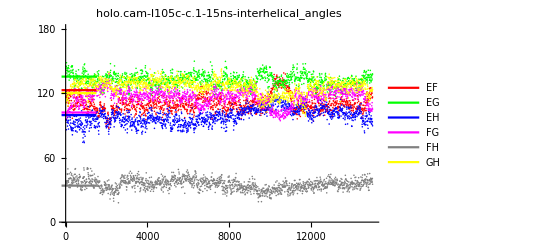

```mathematica
i=1;
j=1;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

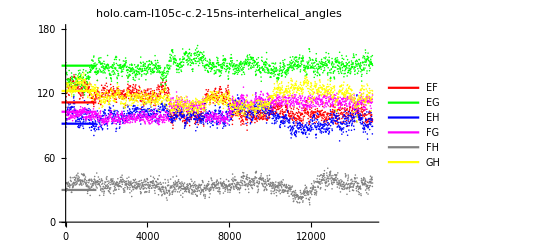

```mathematica
i=1;
j=2;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

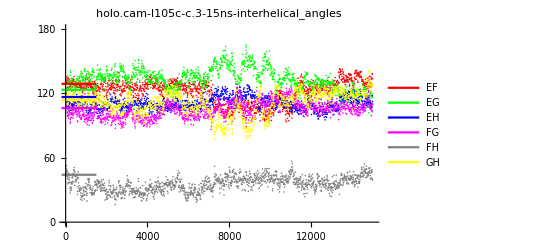

```mathematica
i=1;
j=3;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

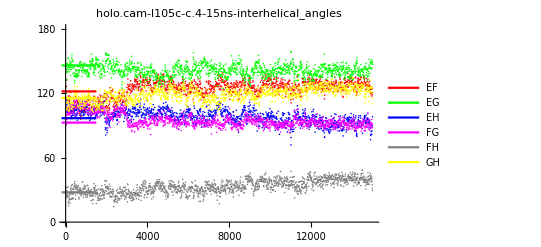

```mathematica
i=1;
j=4;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

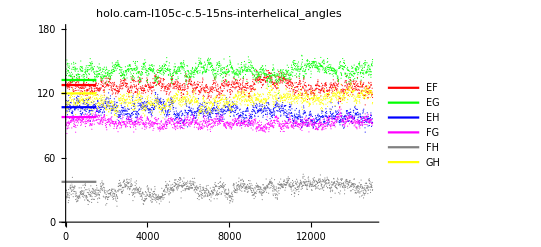

```mathematica
i=1;
j=5;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{{Red,PointSize[0.002]},{Green,PointSize[0.002]},{Blue,PointSize[0.002]},{Magenta,PointSize[0.002]},{Gray,PointSize[0.002]},{Yellow,PointSize[0.002]}}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

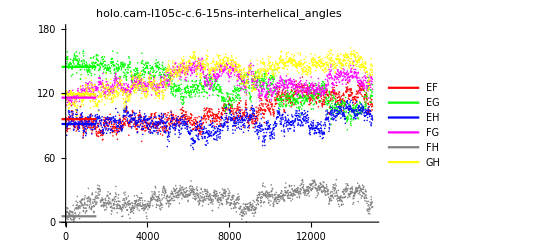

```mathematica
i=1;
j=6;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

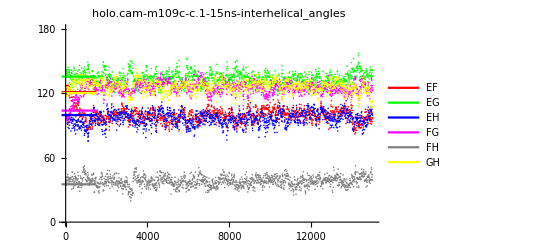

```mathematica
i=2;
j=1;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

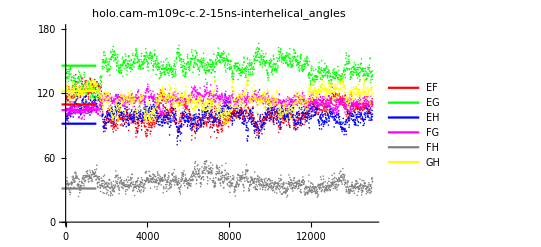

```mathematica
i=2;
j=2;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

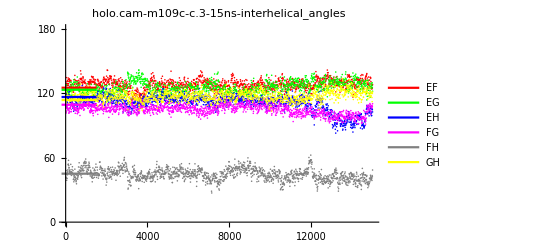

```mathematica
i=2;
j=3;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

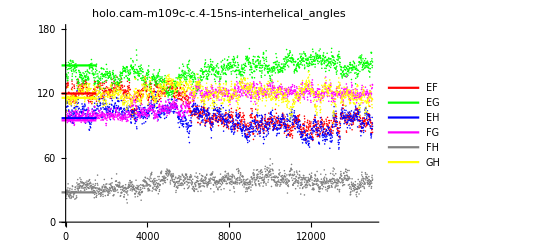

```mathematica
i=2;
j=4;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

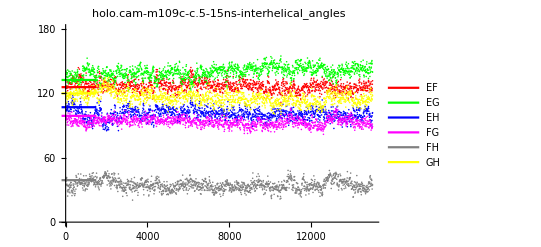

```mathematica
i=2;
j=5;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

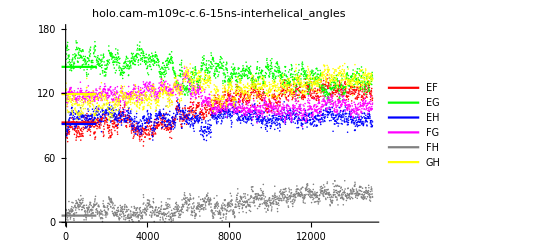

```mathematica
i=2;
j=6;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

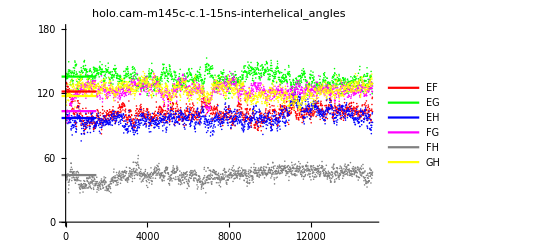

```mathematica
i=3;
j=1;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

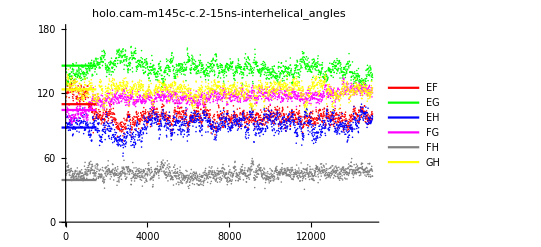

```mathematica
i=3;
j=2;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

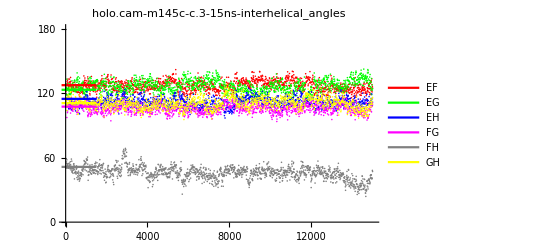

```mathematica
i=3;
j=3;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

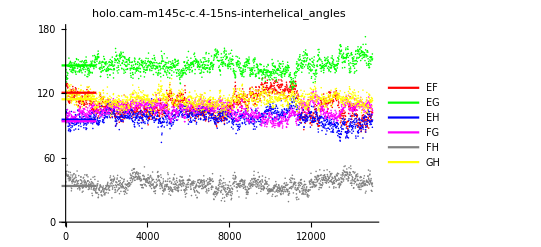

```mathematica
i=3;
j=4;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

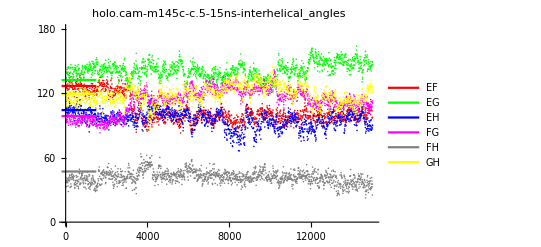

```mathematica
i=3;
j=5;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

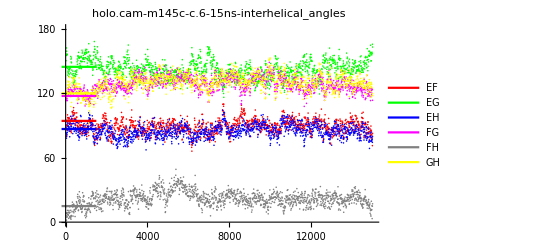

```mathematica
i=3;
j=6;
Show[ListPlot[Table[AngleTraj[[i]][[j]][[k]],{k,1,6}],PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow}],
ListPlot[Table[{{-200,AngleTraj[[i]][[j]][[k]][[1]][[2]]},{1500,AngleTraj[[i]][[j]][[k]][[1]][[2]]}},{k,1,6}],Joined-> True,PlotStyle->{Red,Green,Blue,Magenta,Gray,Yellow},PlotRange->All,PlotStyle->Thickness[0.05],PlotLegends->helixList],PlotLabel->Style[protein<>"-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-15ns-interhelical_angles",FontSize->14,Black],PlotRange->{{0,15000},{0,180}},Ticks-> {Table[m,{m,0,15000,2000}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick,FontSize-> 12]]
```

```mathematica
(*2D distribution plots vs. representative structures*)
```

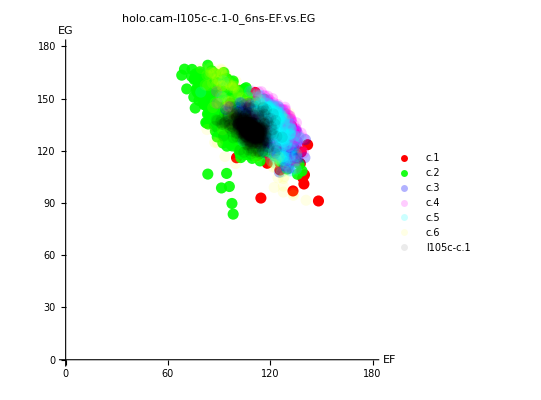

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*);
nse=6;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

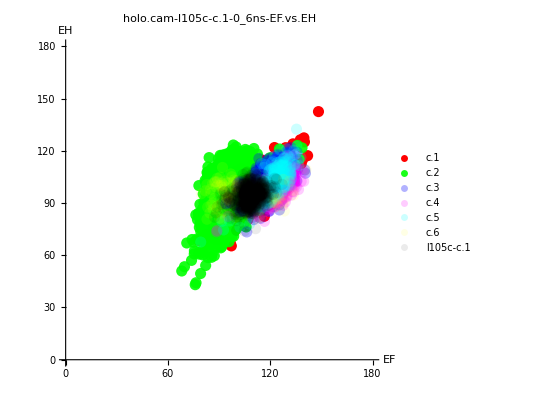

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*);
nse=6;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

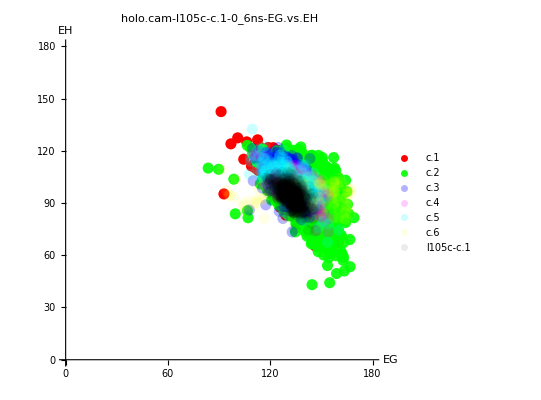

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*)
nse=6;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

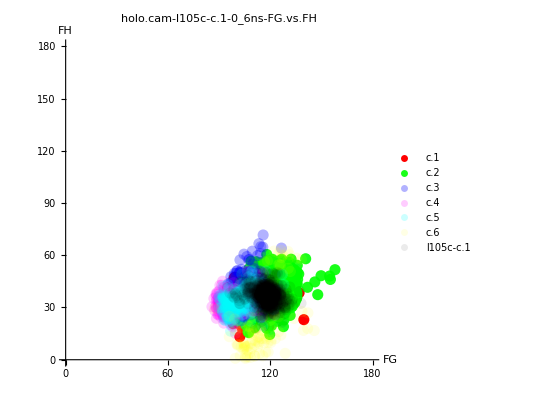

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*)
nse=6;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

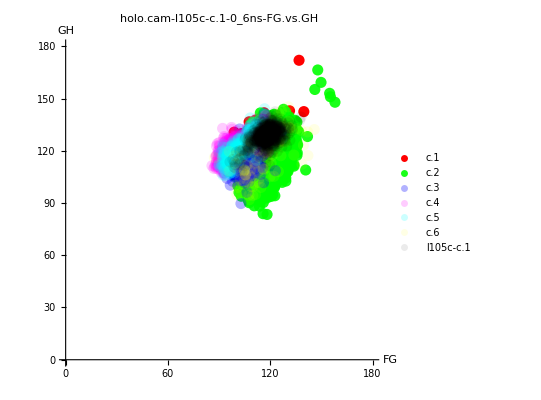

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*)
nse=6;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

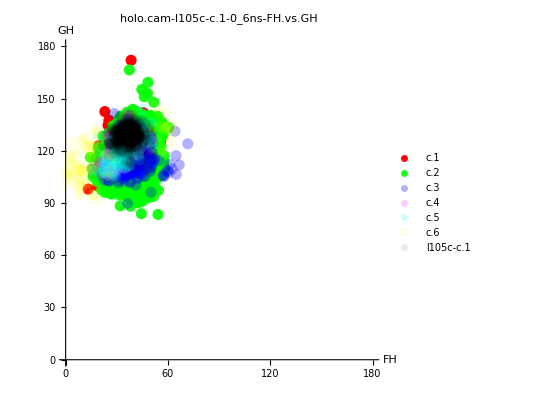

```mathematica
i=1;
j=1;
nsb=0;(*max ns usable*)
nse=6;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

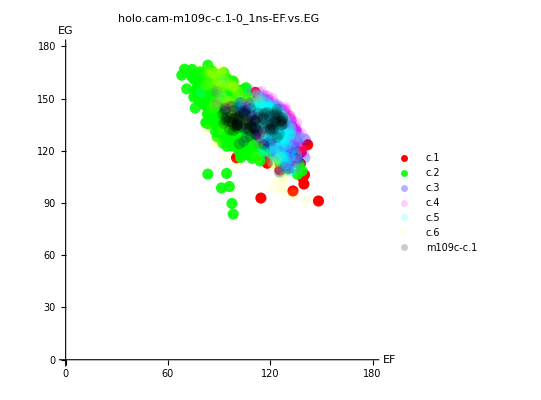

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

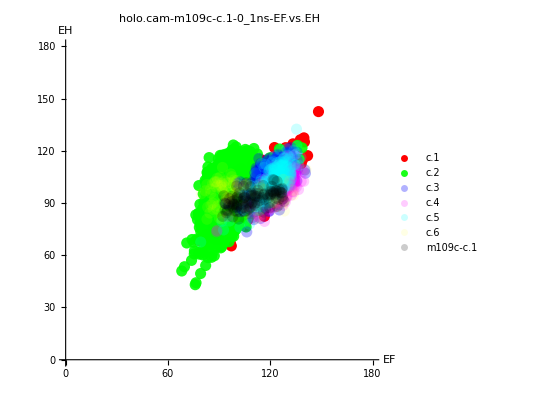

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

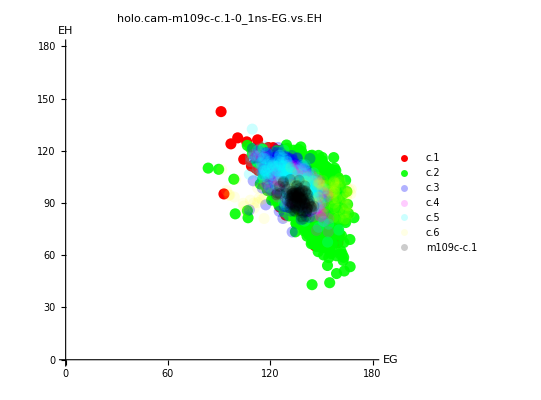

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

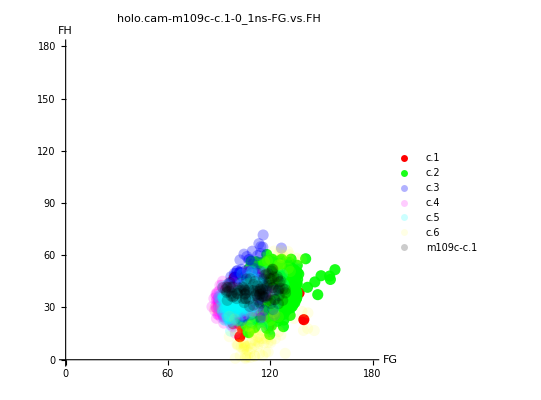

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

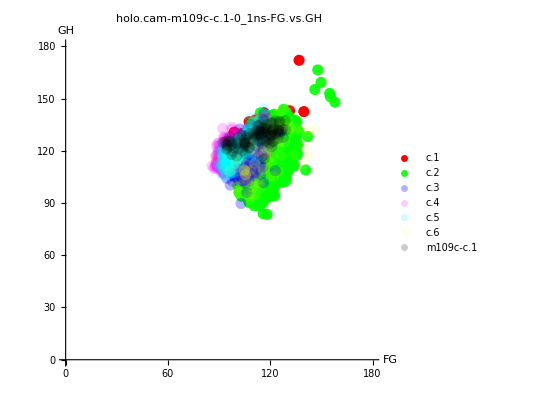

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

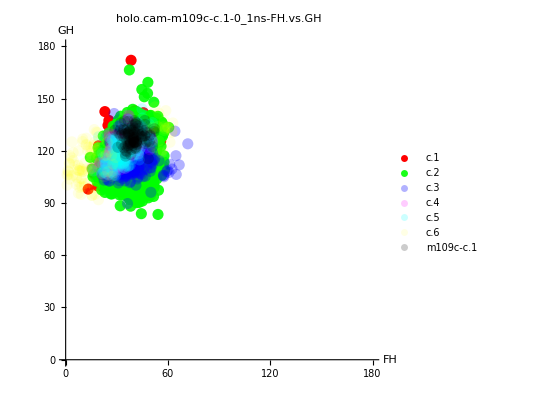

```mathematica
i=2;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

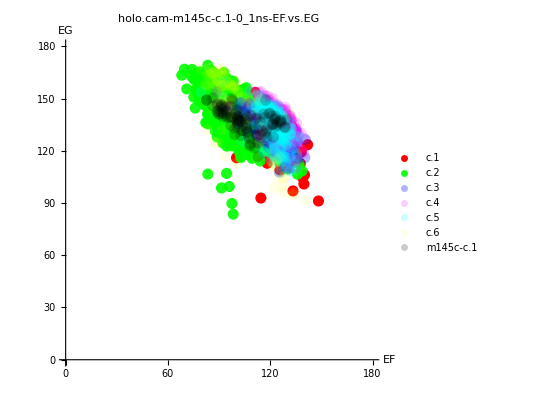

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

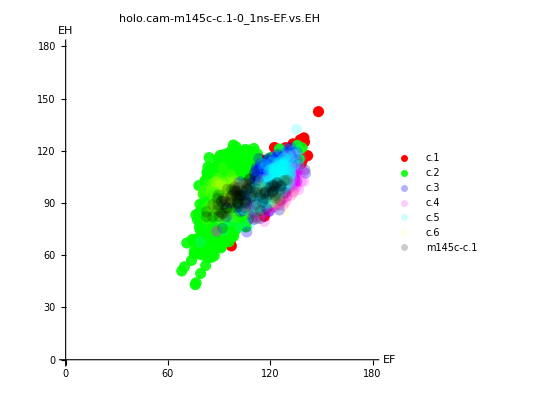

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

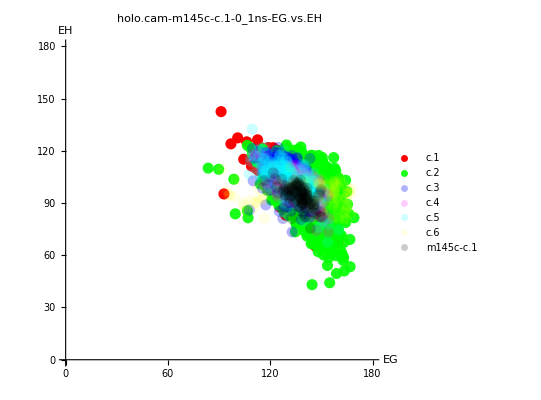

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

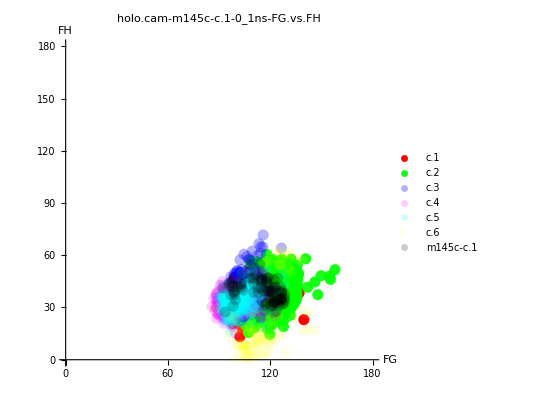

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

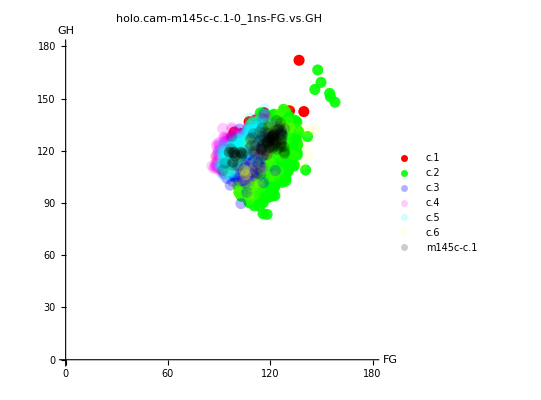

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

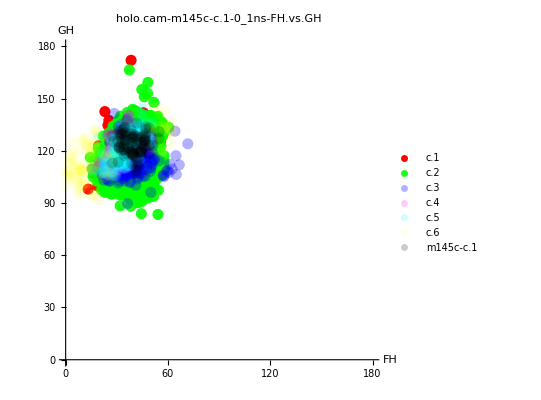

```mathematica
i=3;
j=1;
nsb=0;(*max ns usable*)
nse=1;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

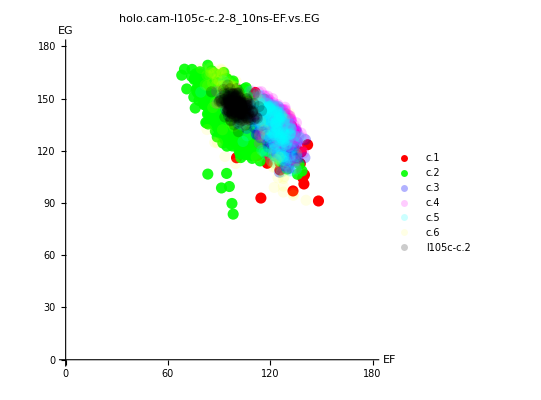

```mathematica
i=1;
j=2;
nsb=8;(*max ns usable*)
nse=10;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

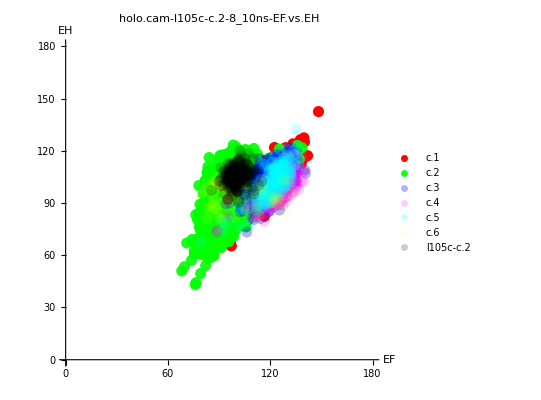

```mathematica
i=1;
j=2;
nsb=8;(*max ns usable*)
nse=10;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

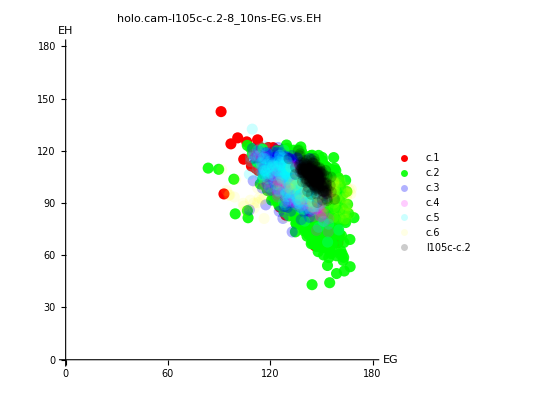

```mathematica
i=1;
j=2;
nsb=8;(*max ns usable*)
nse=10;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

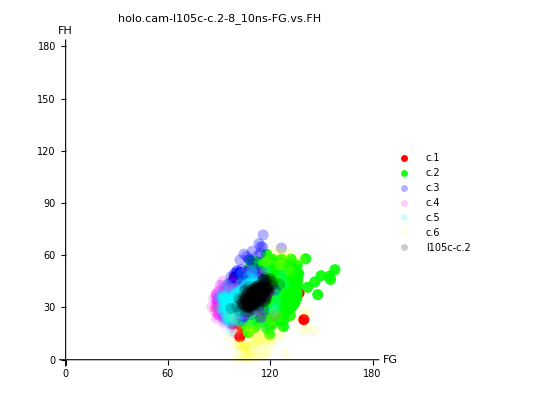

```mathematica
i=1;
j=2;
ns=4;(*max ns usable*)
nsb=8;(*max ns usable*)
nse=10;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

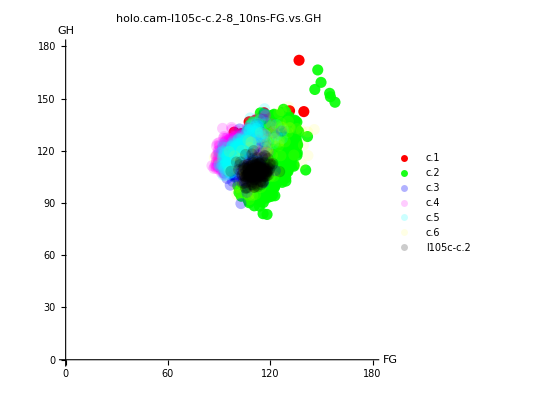

```mathematica
i=1;
j=2;
nsb=8;(*max ns usable*)
nse=10;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

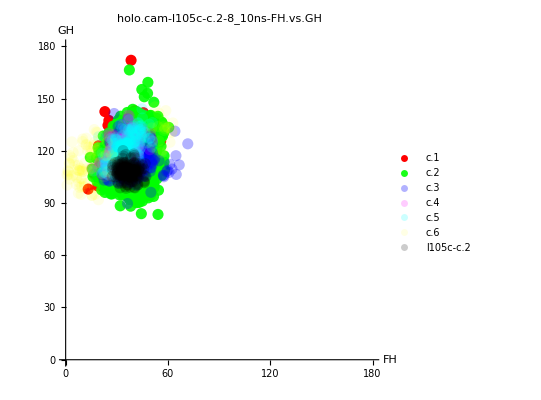

```mathematica
i=1;
j=2;
nsb=8;(*max ns usable*)
nse=10;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

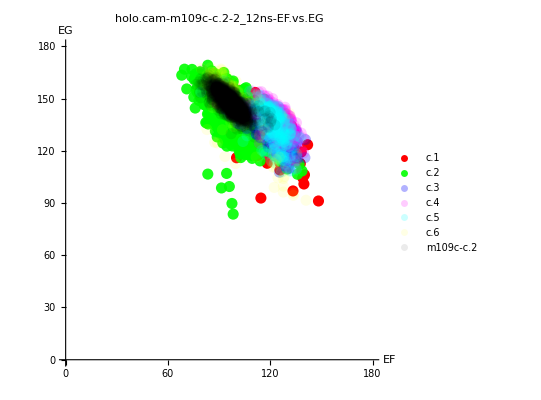

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

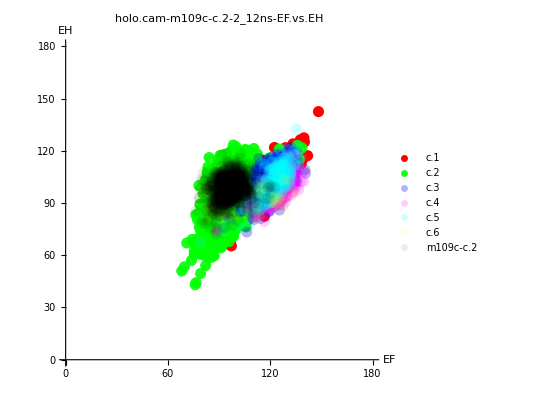

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

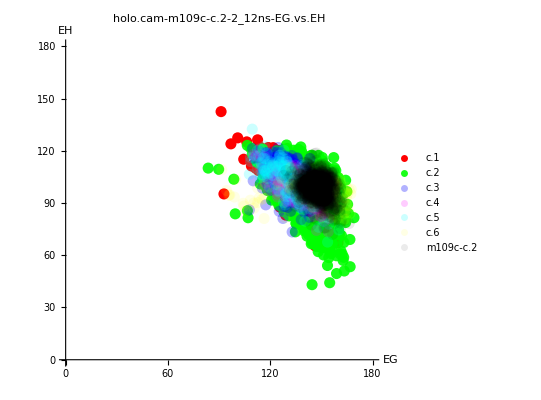

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

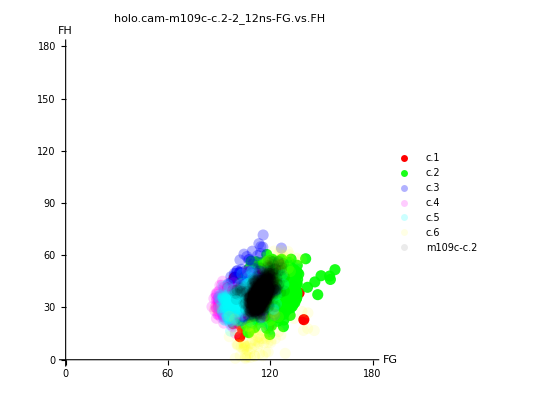

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

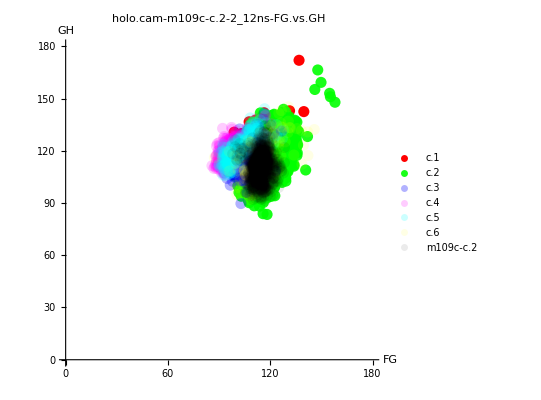

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

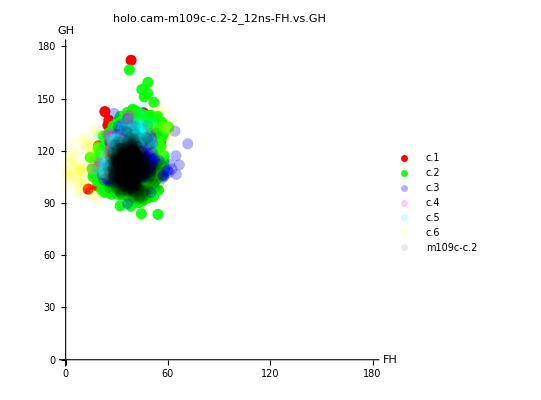

```mathematica
i=2;
j=2;
nsb=2;(*max ns usable*)
nse=12;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

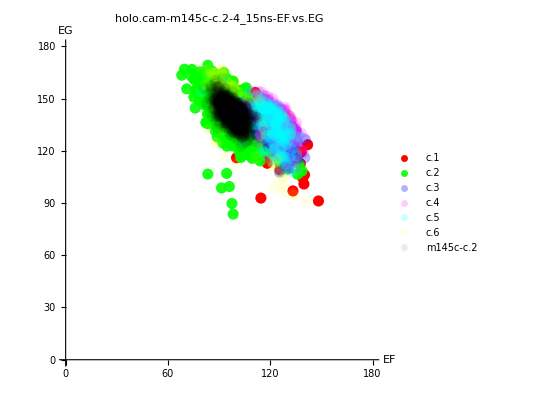

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

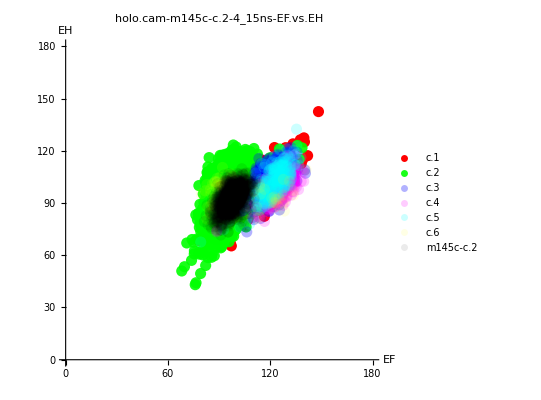

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

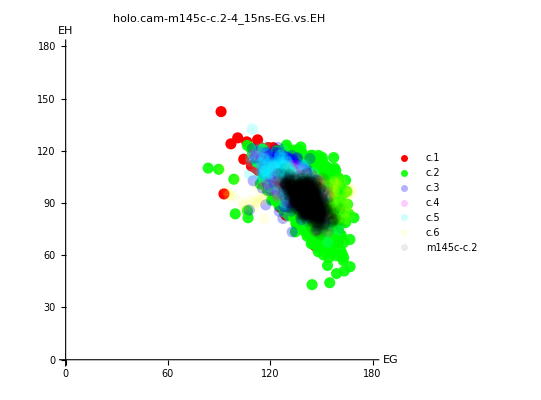

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

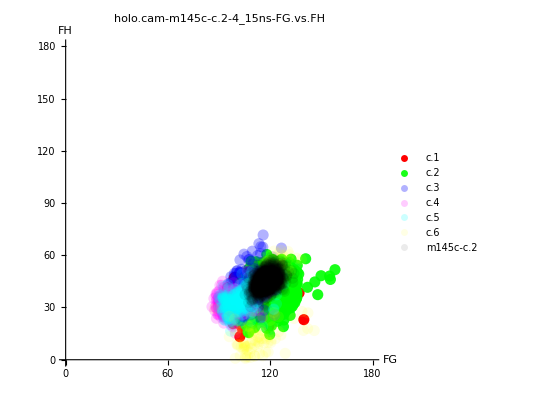

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

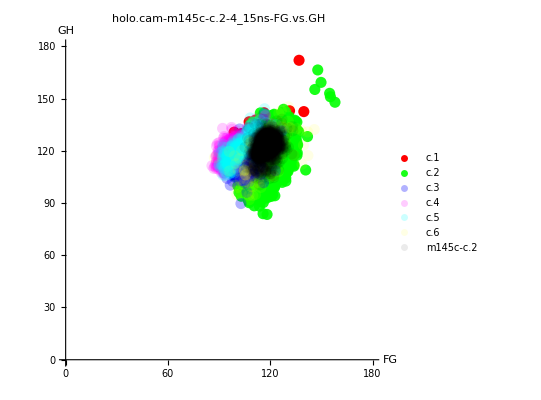

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

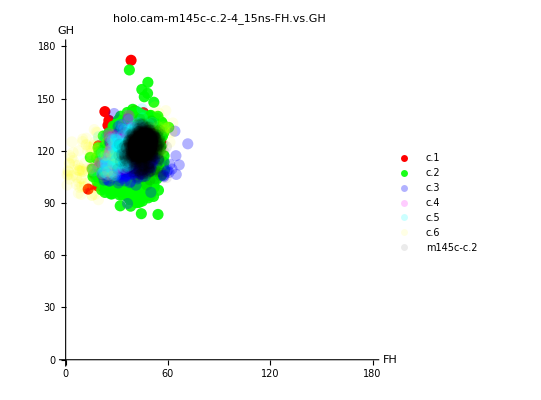

```mathematica
i=3;
j=2;
nsb=4;(*max ns usable*)
nse=15;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

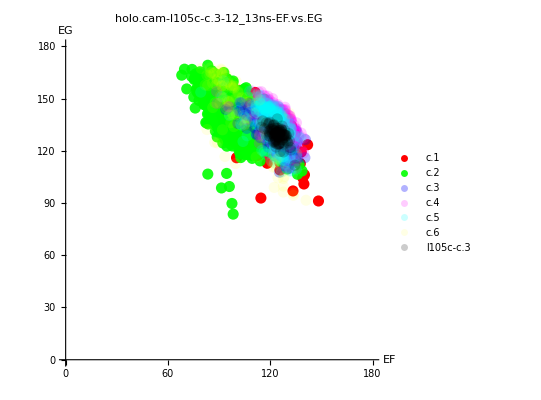

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

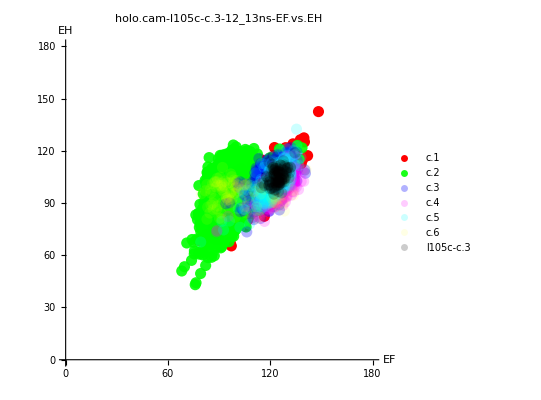

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

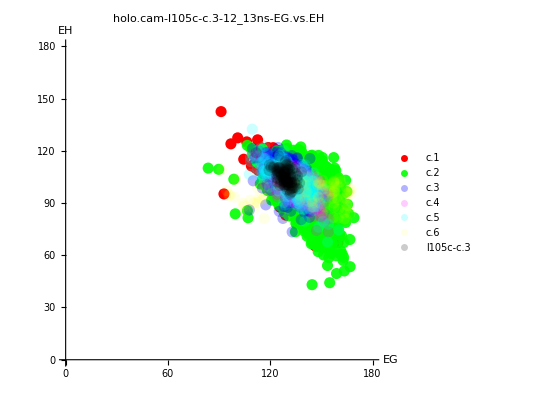

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

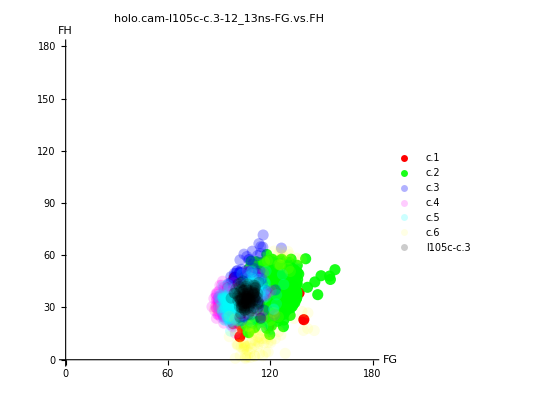

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

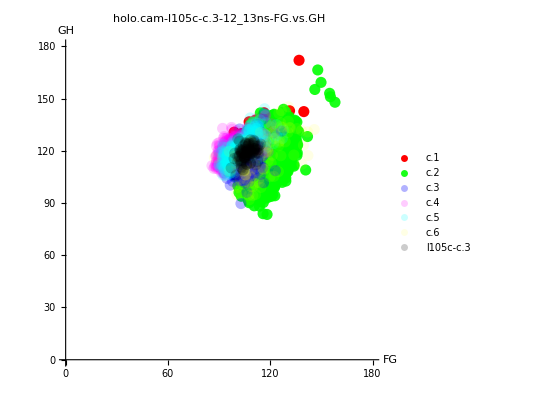

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

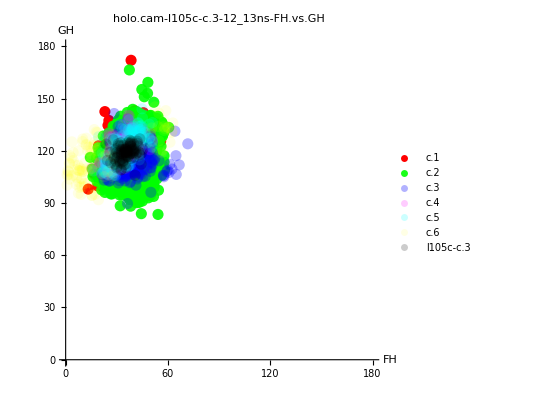

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

```mathematica
i=1;
j=3;
nsb=12;(*max ns usable*)
nse=13;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

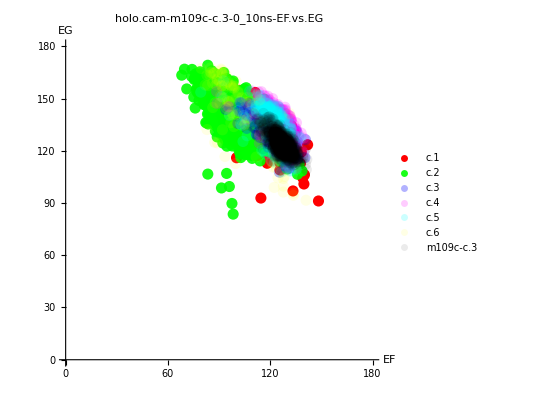

```mathematica
i=2;
j=3;
nsb=0;(*max ns usable*)
nse=10;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

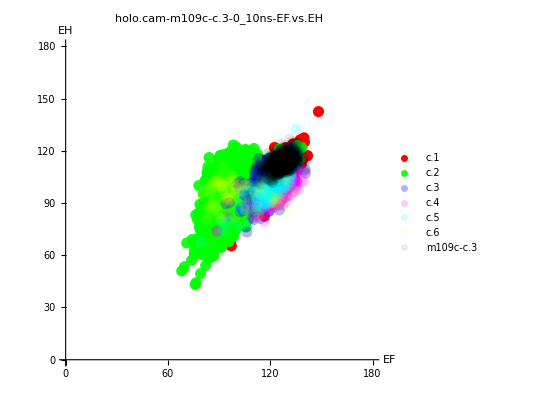

```mathematica
i=2;
j=3;
nsb=0;(*max ns usable*)
nse=10;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

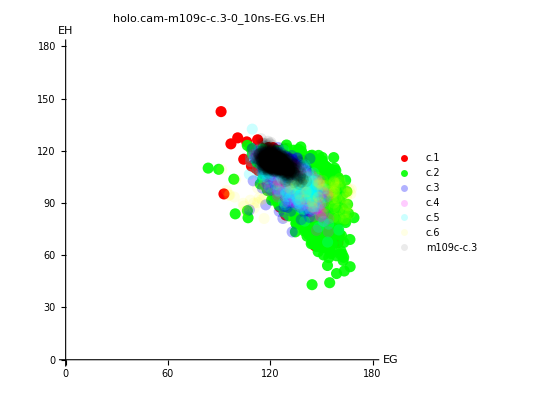

```mathematica
i=2;
j=3;
nsb=0;(*max ns usable*)
nse=10;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

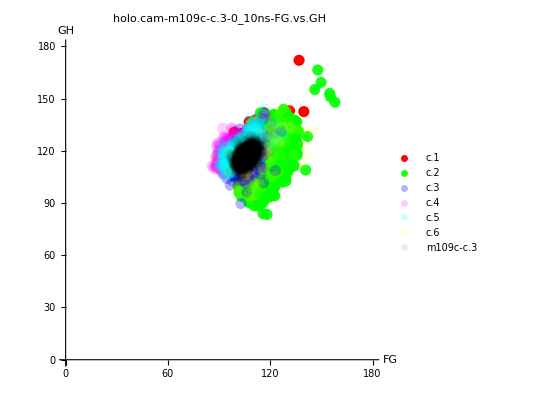

```mathematica
i=2;
j=3;
nsb=0;(*max ns usable*)
nse=10;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

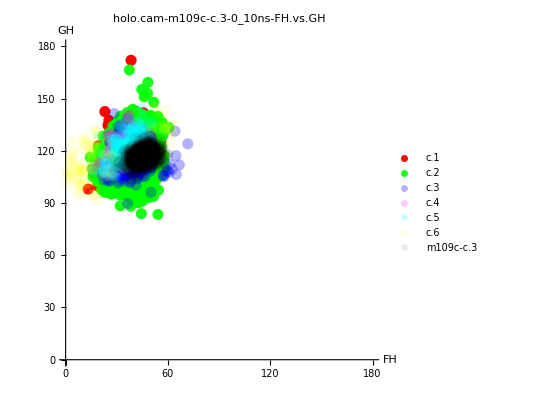

```mathematica
i=2;
j=3;
nsb=0;(*max ns usable*)
nse=10;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

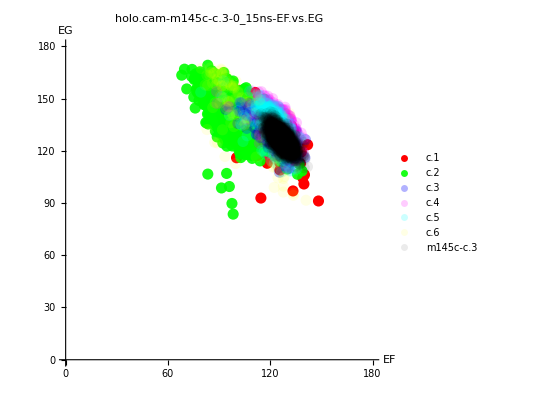

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

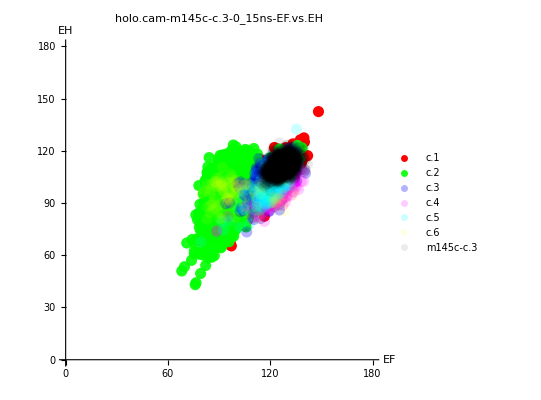

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

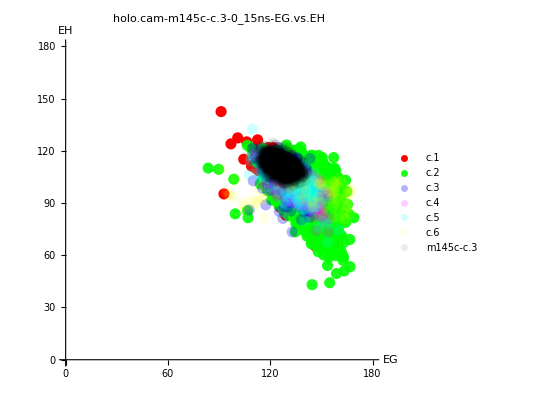

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

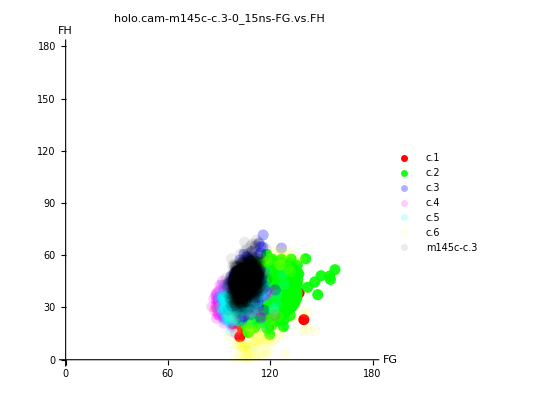

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

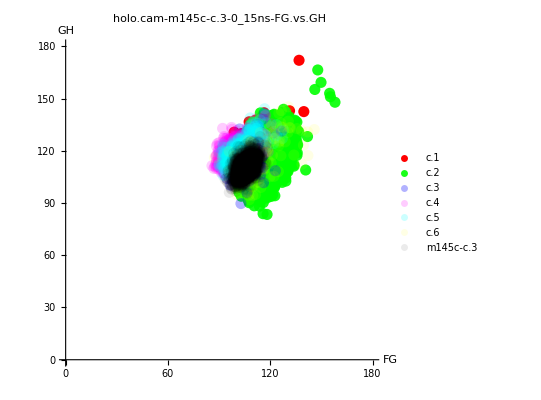

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

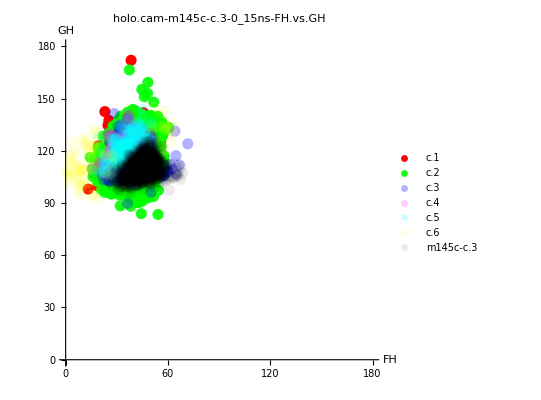

```mathematica
i=3;
j=3;
nsb=0;(*max ns usable*)
nse=15;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

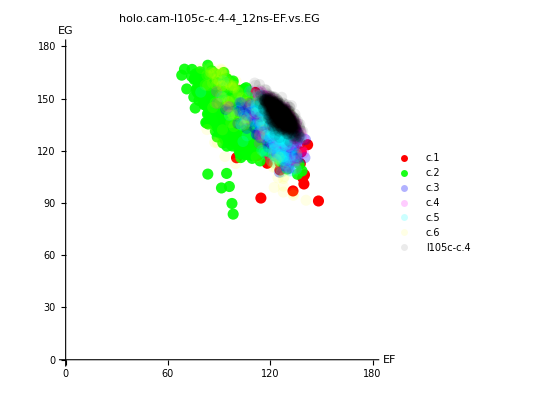

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

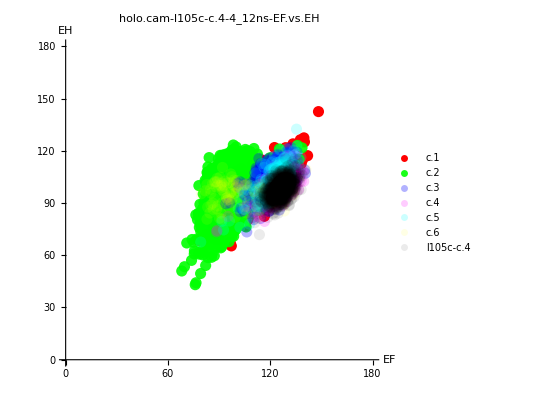

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

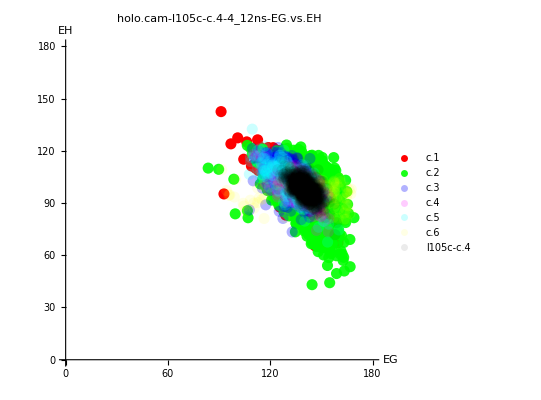

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

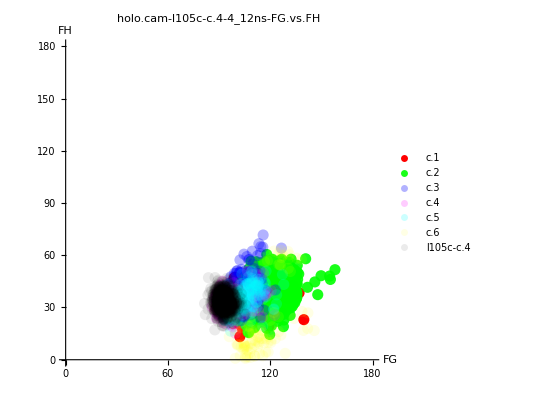

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

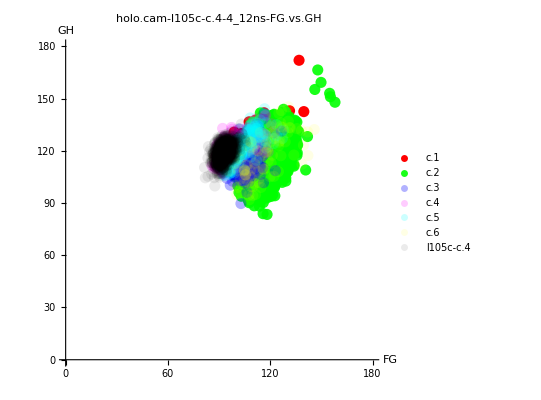

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

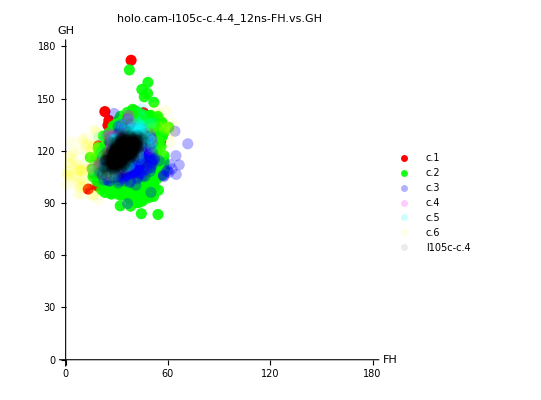

```mathematica
i=1;
j=4;
nsb=4;(*max ns usable*)
nse=12;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

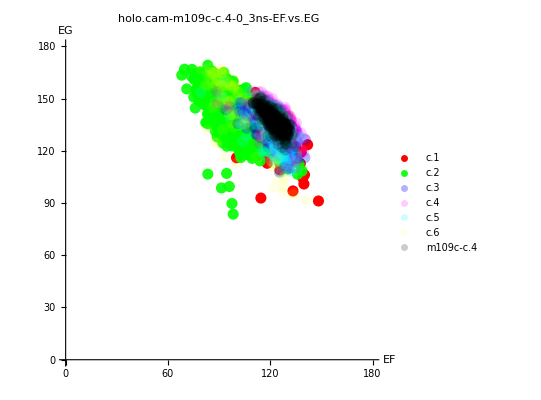

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

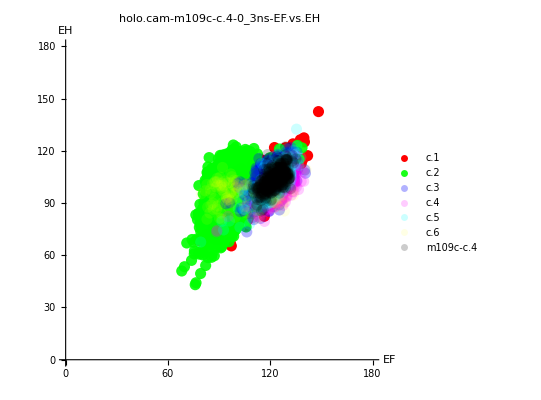

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

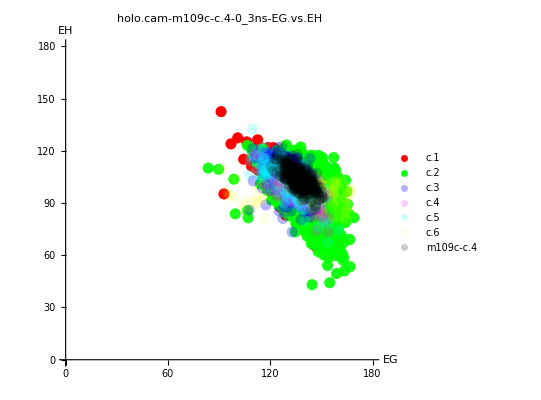

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

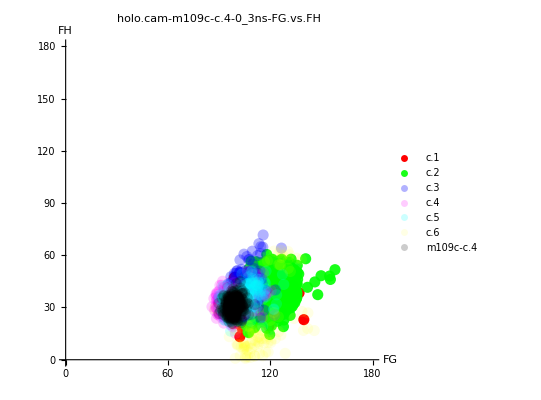

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

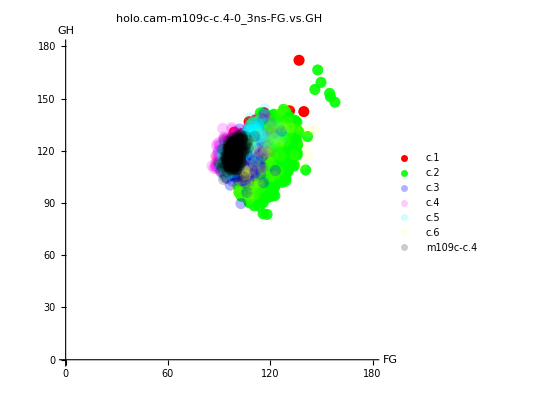

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

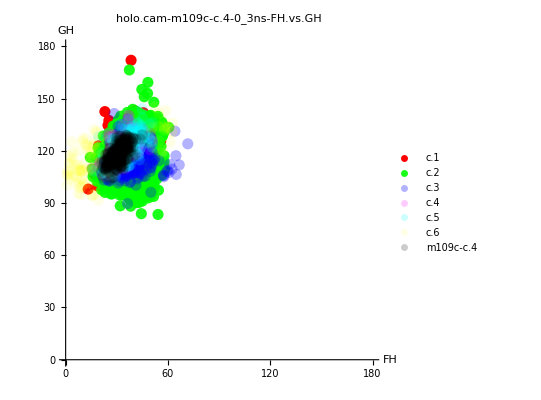

```mathematica
i=2;
j=4;
nsb=0;(*max ns usable*)
nse=3;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

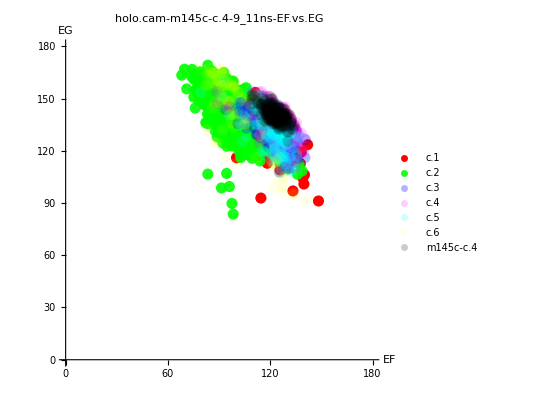

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

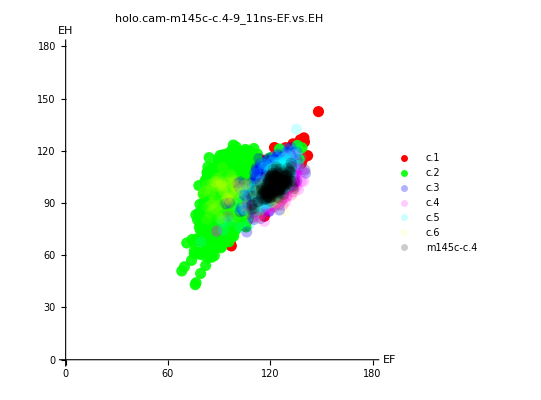

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

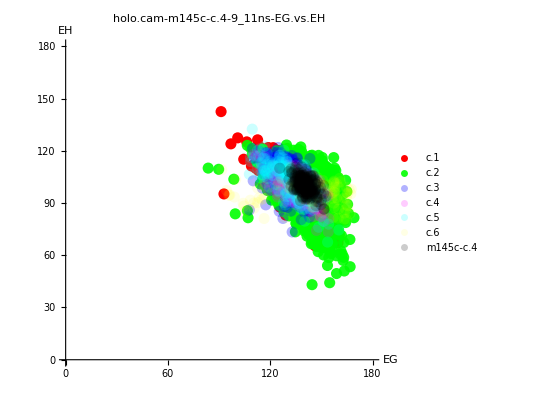

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

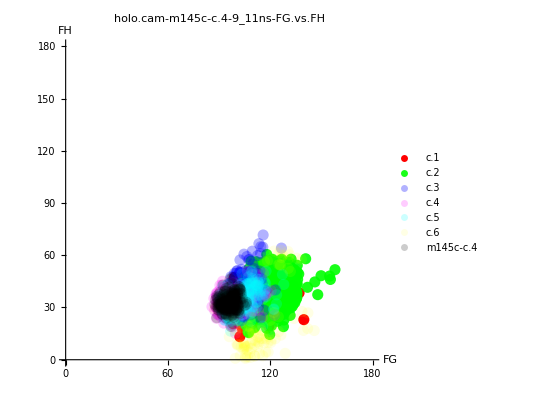

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

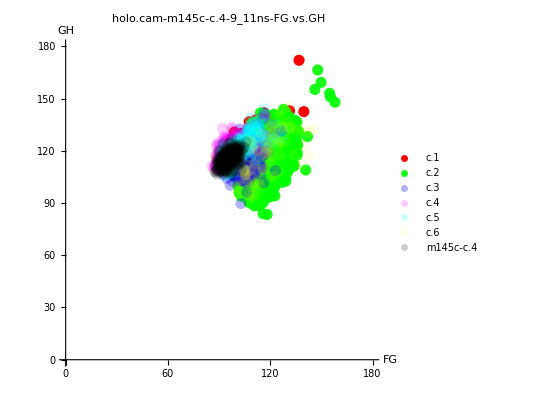

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

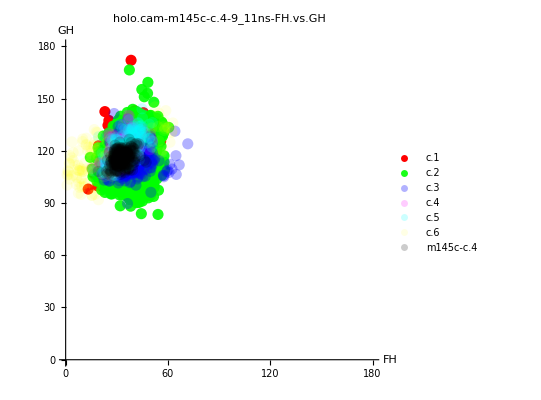

```mathematica
i=3;
j=4;
nsb=9;(*max ns usable*)
nse=11;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

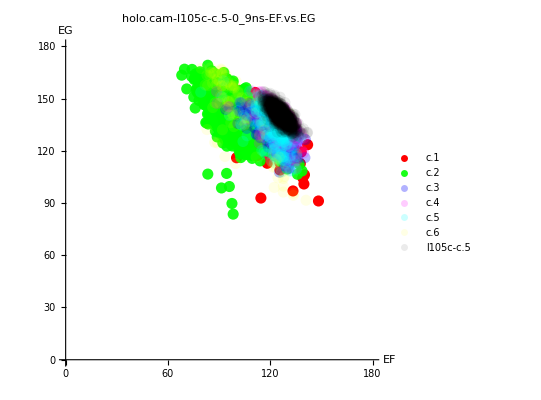

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

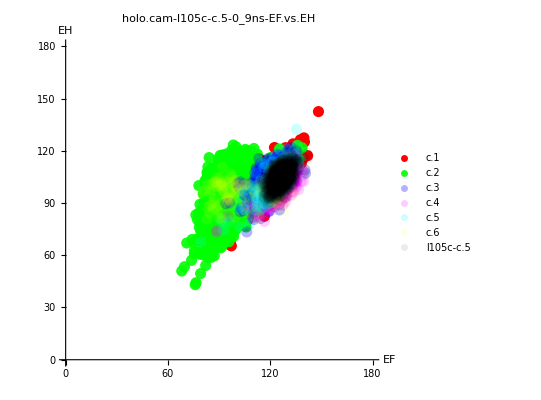

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

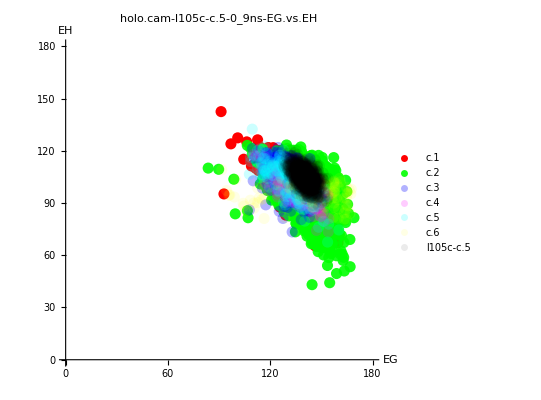

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

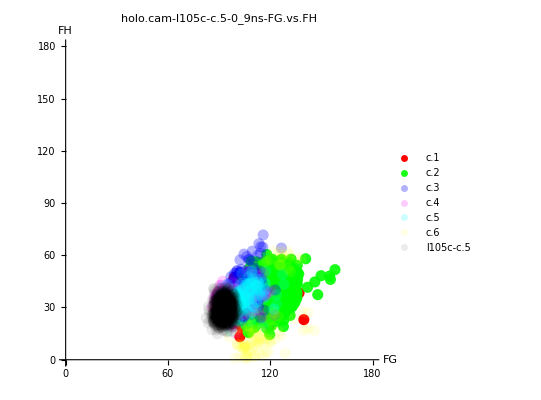

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

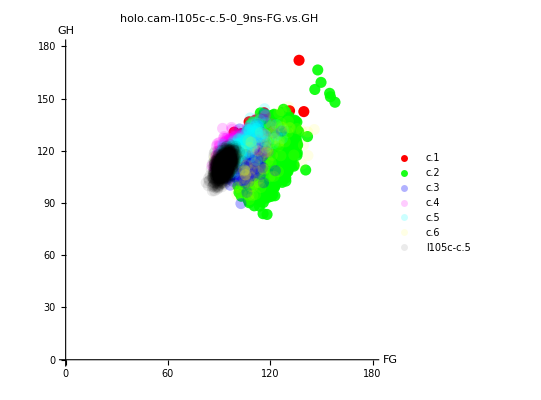

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

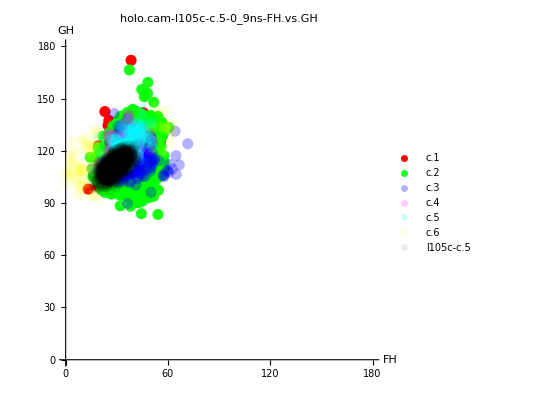

```mathematica
i=1;
j=5;
nsb=0;(*max ns usable*)
nse=9;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

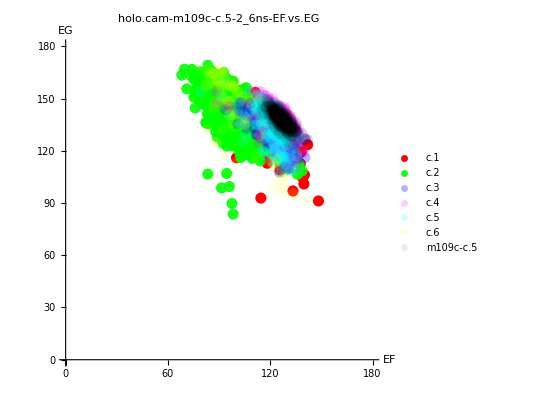

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

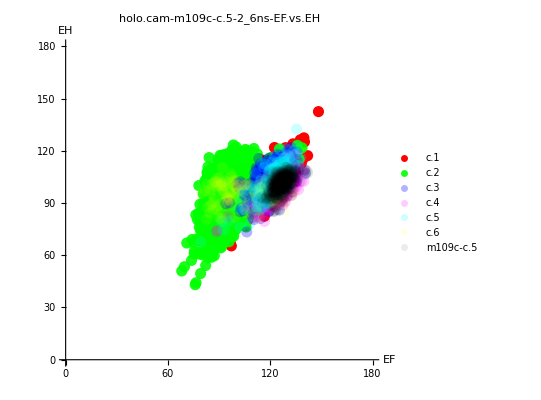

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

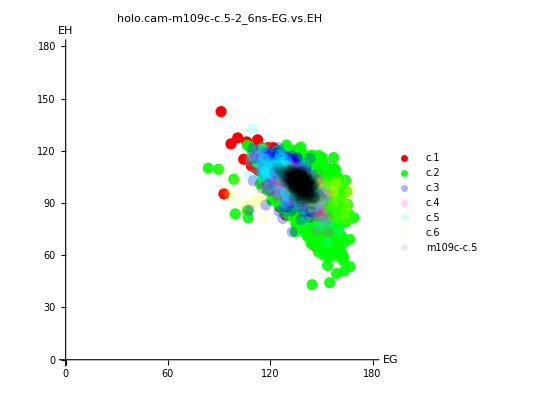

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

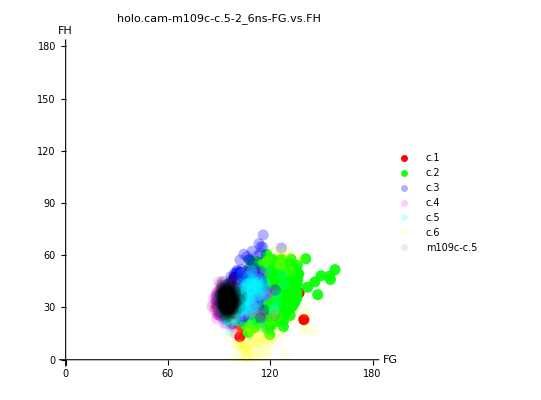

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

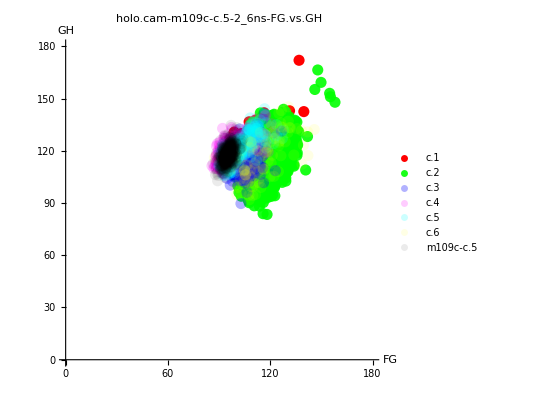

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

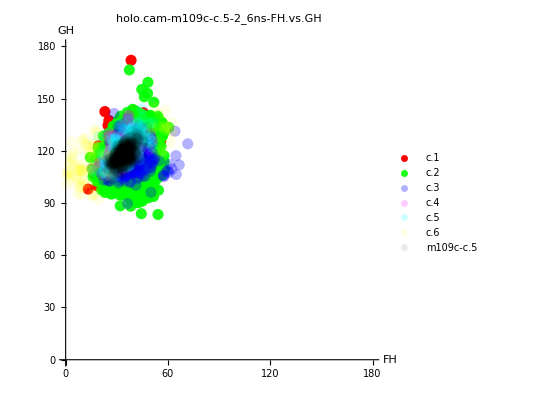

```mathematica
i=2;
j=5;
nsb=2;(*max ns usable*)
nse=6;
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

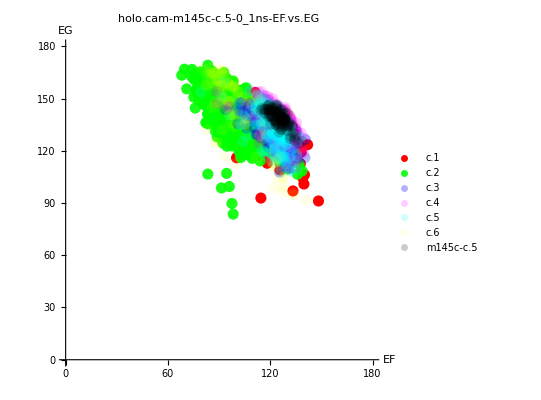

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

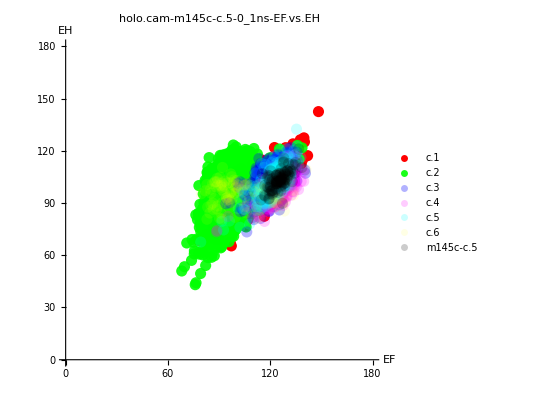

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

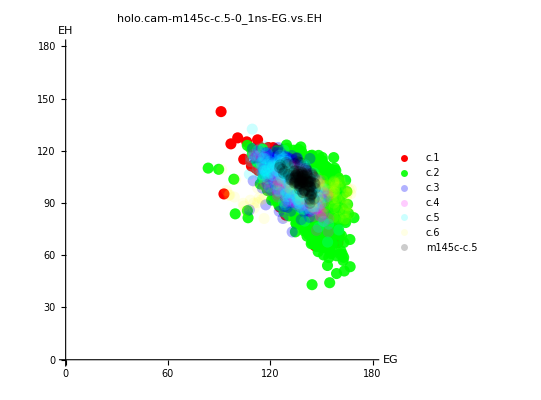

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

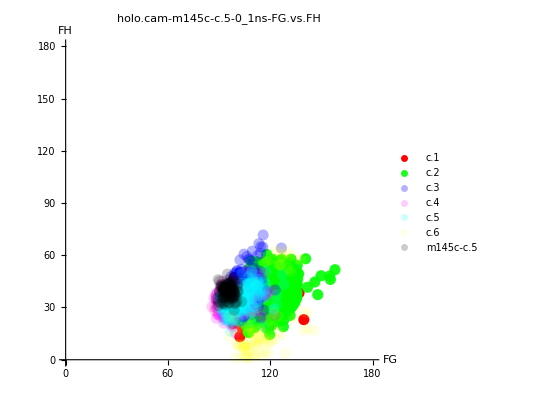

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

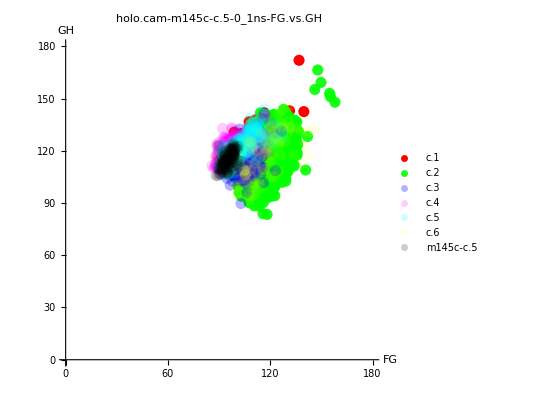

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

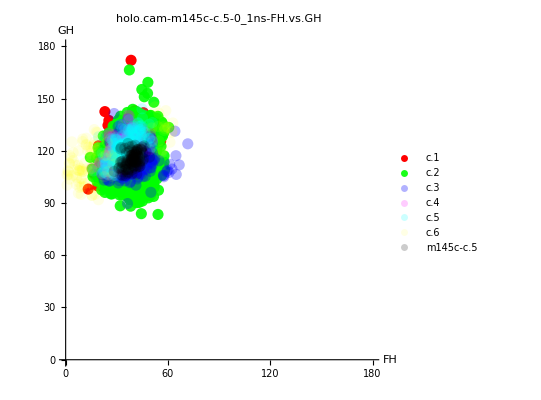

```mathematica
i=3;
j=5;
nsb=0;
nse=1;(*max ns usable*)
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

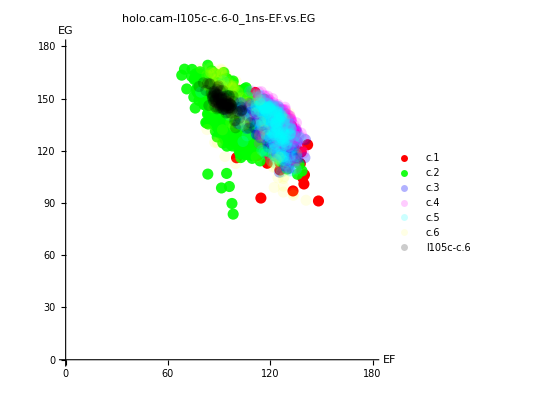

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

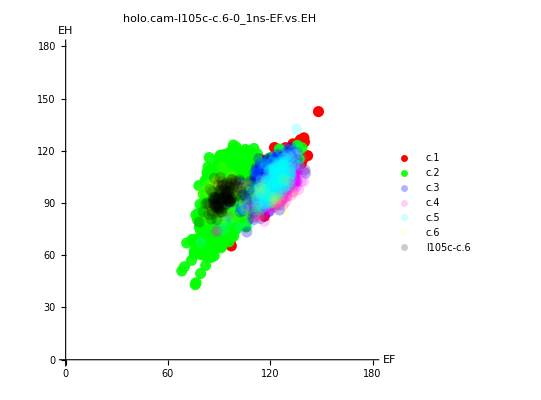

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

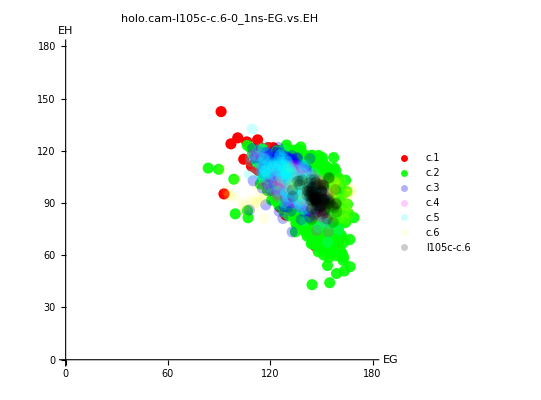

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

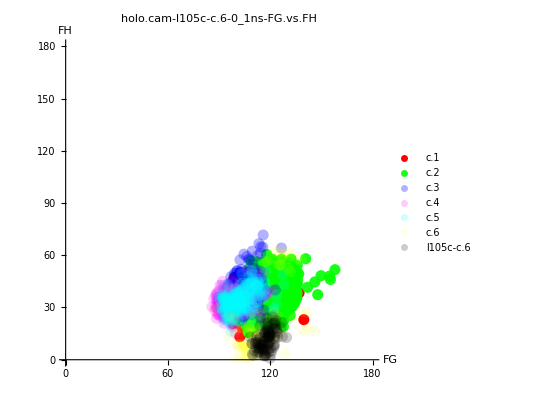

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

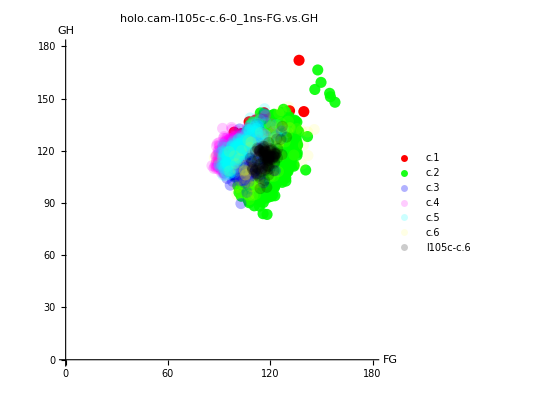

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

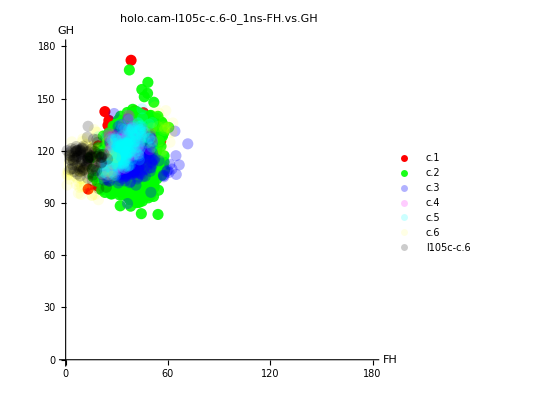

```mathematica
i=1;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

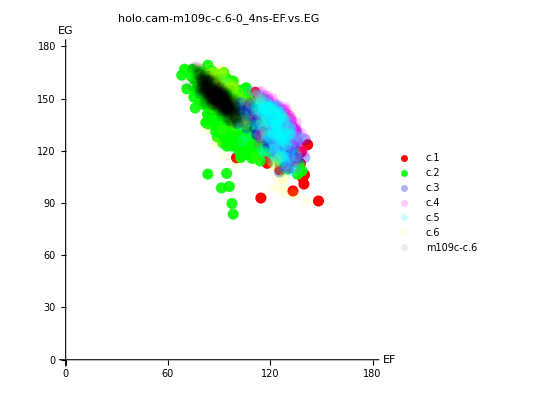

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

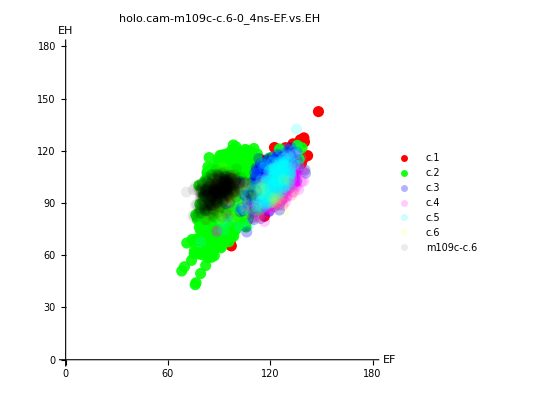

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

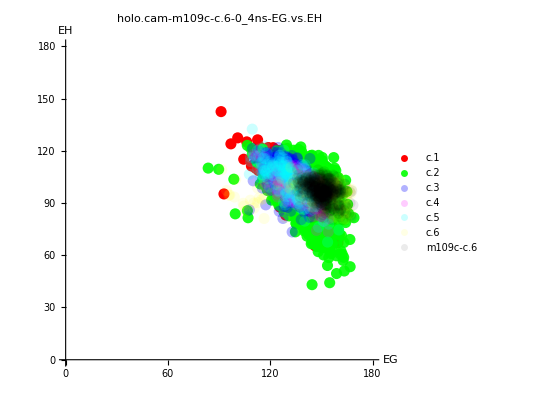

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

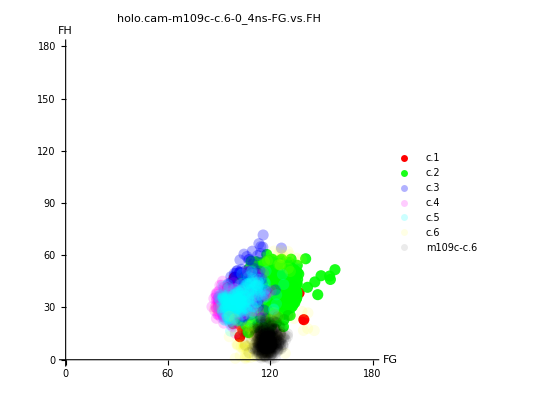

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

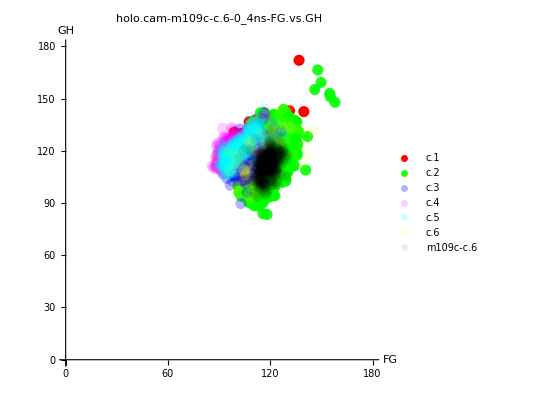

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

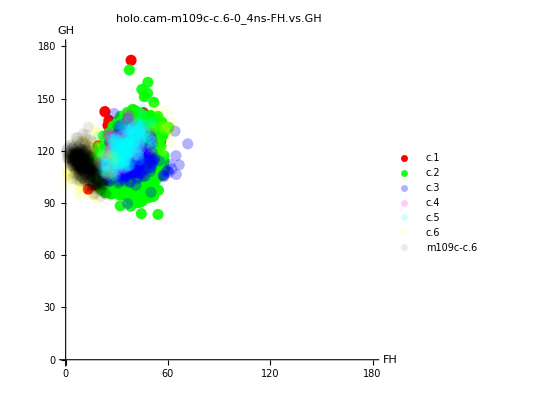

```mathematica
i=2;
j=6;
nsb=0;
nse=4;(*max ns usable*)
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.08],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=2;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=1;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=2;
k2=3;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=5;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=4;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-

```mathematica
i=3;
j=6;
nsb=0;
nse=1;(*max ns usable*)
k1=5;
k2=6;
Show[
ListPlot[Table[Partition[Riffle[AngleRep[[j]][[k1]][[;;,2]],AngleRep[[j]][[k2]][[;;,2]]],2],{j,1,6}],PlotStyle-> {{Red,Opacity[1], PointSize[0.02]},{Green,Opacity[0.9], PointSize[0.02]},{Blue,Opacity[0.3], PointSize[0.02]},{Magenta,Opacity[0.2], PointSize[0.02]},{Cyan,Opacity[0.2], PointSize[0.02]},{Yellow,Opacity[0.1], PointSize[0.02]}},PlotLegends->spointList],ListPlot[Partition[Riffle[AngleTraj[[i]][[j]][[k1]][[nsb*100+1;;nse*100,2]],AngleTraj[[i]][[j]][[k2]][[nsb*100+1;;nse*100,2]]],2],PlotStyle->{Black,Opacity[0.2],PointSize[0.02]},PlotLegends->{siteList[[i]]<>"-"<>spointList[[j]]}],PlotLabel->Style["holo.cam-"<>siteList[[i]]<>"-"<>spointList[[j]]<>"-"<>ToString[nsb]<>"_"<>ToString[nse]<>"ns-"<>helixList[[k1]]<>".vs."<>helixList[[k2]],FontSize->16,Black],PlotRange->{{0,180},{0,180}},AxesOrigin-> {0,0},AspectRatio-> 1,AxesLabel-> {helixList[[k1]],helixList[[k2]]},AxesStyle->Directive[Black,16],Ticks-> {Table[m,{m,0,180,30}],Table[n,{n,0,180,30}]},TicksStyle-> Directive[Black,Thick]]
```

-Graphics-